```mathematica
a=1;
s=1;
jnm=-0.5;
jab=1;
jd=0.0;
kz=0.01;
bz=0.0025;
```

```mathematica
f[kx_,ky_]:=s*(2*jnm*Cos[2*kx*a]+2*jd*Cos[2*ky*a]-2*(jd+jnm))+4*s*jab+2*s*kz+bz
r2[kx_,ky_,d_]:=2*s*d*Sin[kx*a]*Sin[ky*a]
r1[kx_,ky_]:=2*jab*s*(Cos[kx*a+ky*a]+Cos[kx*a-ky*a])
h[kx_,ky_]:=s*(2*jnm*Cos[2*ky*a]+2*jd*Cos[2*kx*a]-2*(jd+jnm))+4*s*jab+2*s*kz-bz
```

```mathematica
ω[kx_,ky_,d_]:=0.5*Sqrt[(f[kx,ky]+h[kx,ky])^2-4*(r1[kx,ky]*r1[kx,ky]+r2[kx,ky,d]*r2[kx,ky,d])]
δ[kx_,ky_]:=0.5*(f[kx,ky]-h[kx,ky])
```

```mathematica
Eα[kx_,ky_,d_]:=ω[kx,ky,d]+δ[kx,ky]
Eβ[kx_,ky_,d_]:=ω[kx,ky,d]-δ[kx,ky]
Eα[x,y,0.001]==Eα[-x,-y,0.001]
```

True

```mathematica
Plot3D[{Eα[kx,ky,0.001],-Eβ[kx,ky,0.001]},{kx,-π/2a,π/2a},{ky,-π/2a,π/2a},
AxesLabel->{Style["ak_x",Bold,25],Style["ak_y",Bold,20],Style["E/SJ_AB",Bold,20]},
PlotStyle->{Red,Lightblue,Thick},
ImageSize->Large,
Ticks->{{-Pi/2a,0,Pi/2a},{-Pi/2a,0,Pi/2a},{-6,-3,0,3,6}},
AxesStyle->Directive[Black,20],
PlotTheme->"Scientific",
Boxed->False,
PlotPoints->50]
```

-Graphics3D-

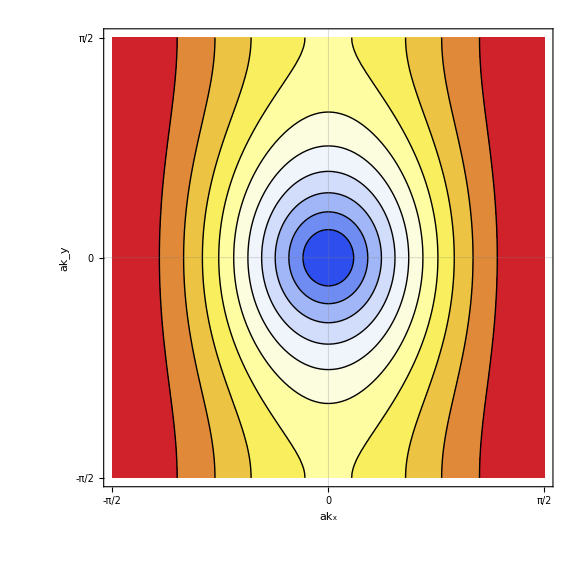

```mathematica
ContourPlot[Eα[kx,ky,0.001],{kx,-π/2a,π/2a},{ky,-π/2a,π/2a},
ColorFunction->"TemperatureMap",
PlotPoints->50,
ImageSize->Large,
PlotRange->Full,
Contours->10,
Axes->True,
AxesLabel->{Style["ak_x",Bold,20],Style["ak_y",Bold,20]},
FrameTicks->{{-Pi/2a,0,Pi/2a},{-Pi/2a,0,Pi/2a}},
LabelStyle->{20,Black},
PlotTheme->"Scientific"]
```

```mathematica
Plot3D[{Eα[kx,ky,0.001],Eβ[kx,ky,0.001]},{kx,-π/2a,π/2a},{ky,-π/2a,π/2a},
AxesLabel->{Style["ak_x",Bold,25],Style["ak_y",Bold,20],Style["E/SJ_AB",Bold,20]},
PlotStyle->{Red,Lightblue,Thick},
ImageSize->Large,
Ticks->{{-Pi/2a,0,Pi/2a},{-Pi/2a,0,Pi/2a},{0,4}},
AxesStyle->Directive[Black,Thickness[0.0025],20],
PlotTheme->"Scientific",
PlotPoints->50,
AxesOrigin->{0,0,0},
Boxed->False,
FaceGrids->{{{0,0,-1},{{π/2a,π/4a,0,-π/4a,π/2a},{π/2a,π/4a,0,-π/4a,-π/2a}}}}]
```

-Graphics3D-

```mathematica
ϕ[kx_,ky_,d_]:=ArcTan[r2[kx,ky,d]/r1[kx,ky]]
θ[kx_,ky_,d_]:=ArcCosh[(f[kx,ky]+h[kx,ky])/(2*ω[kx,ky,d])]
```

```mathematica
F[kx_,ky_,d_]=0.5*Sinh[θ[kx,ky,d]]*(D[θ[kx,ky,d],kx]*D[ϕ[kx,ky,d],ky]-D[θ[kx,ky,d],ky]*D[ϕ[kx,ky,d],kx]);
NIntegrate[F[kx,ky,0.001],{kx,-π/2a,π/2a},{ky,-π/2a,π/2a}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.02324×10^-20 and 1.62936×10^-16 for the integral and error estimates.

-2.02324×10^-20

```mathematica
Plot3D[F[kx,ky,0.001],{kx,-π/2a,π/2a},{ky,-π/2a,π/2a},
AxesLabel->{Style["ak_x",Bold,20],Style["ak_y",Bold,20],Style["(F^α)_xy",Bold,20]},
Ticks->{{-Pi/2a,0,Pi/2a},{-Pi/2a,0,Pi/2a},{0.0005,0,-0.0005}},
ColorFunction->"TemperatureMap",
PlotPoints->50,
ImageSize->Large,
PlotRange->Full,
AxesStyle->Directive[Black,20],
PlotTheme->"Scientific"]
```

-Graphics3D-

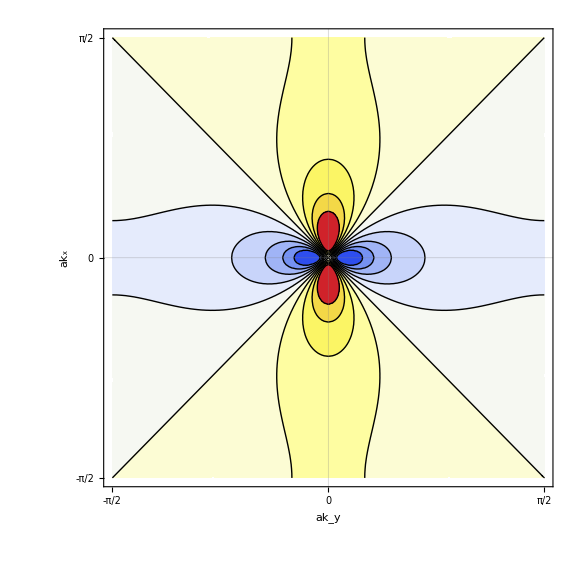

```mathematica
ContourPlot[F[kx,ky,0.001],{kx,-π/2a,π/2a},{ky,-π/2a,π/2a},
ColorFunction->"TemperatureMap",
PlotPoints->50,
ImageSize->Large,
PlotRange->Full,
Contours->10,
Axes->True,
AxesLabel->{Style["ak_y",Bold,23],Style["ak_x",Bold,23]},
FrameTicks->{{-Pi/2a,0,Pi/2a},{-Pi/2a,0,Pi/2a}},
LabelStyle->{20,Black},
PlotTheme->"Scientific"]
```

```mathematica
σ[T_,d_]:=NIntegrate[-F[kx,ky,d]*(Coth[Eα[kx,ky,d]/(2*T)]+Coth[Eβ[kx,ky,d]/(2*T)])/(8*π*π),{kx,-π/2a,π/2a},{ky,-π/2a,π/2a}]
```

```mathematica
Tlist=Array[#&,30,{0.00001,3}];
dlist={0.001,0.003,0.005,0.007};
Parallelize[
σ1=σ[Tlist,dlist[[1]]];σ2=σ[Tlist,dlist[[2]]];σ3=σ[Tlist,dlist[[3]]];σ4=σ[Tlist,dlist[[4]]];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.23289×10^-23 and 4.12898×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.78628×10^-12 and 1.93318×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.07401×10^-20 and 9.37551×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

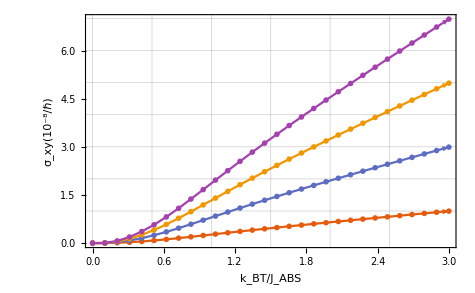

```mathematica
ListPlot[{Transpose[{Tlist,σ1/0.00000001}],Transpose[{Tlist,σ2/0.00000001}],Transpose[{Tlist,σ3/0.00000001}],Transpose[{Tlist,σ4/0.00000001}]},
Filling->None,
Joined->True,
PlotStyle->{
Arrowheads[{{0.7,0.7,Graphics[Text[Framed[Style["D=0.001×J_ABS",18],Background->White,FrameStyle->None]]]}}],
Arrowheads[{{0.7,0.7,Graphics[Text[Framed[Style["D=0.003×J_ABS",18],Background->White,FrameStyle->None]]]}}],
Arrowheads[{{0.7,0.7,Graphics[Text[Framed[Style["D=0.005×J_ABS",18],Background->White,FrameStyle->None]]]}}],
Arrowheads[{{0.7,0.7,Graphics[Text[Framed[Style["D=0.007×J_ABS",18],Background->White,FrameStyle->None]]]}}]},
PlotMarkers->{Style["x",Opacity[0.17],17]},
FrameLabel->{Style["k_BT/J_ABS",Bold,20],Style["σ_xy(10^-8/ℏ)",Bold,20]},
ImageSize->Large,
LabelStyle->{20,Black},
PlotTheme->"Scientific",
GridLines->{{0,0.5,1,1.5,2,2.5},{1,2,3,4,5,6,7}}]/.Line->Arrow
```